# Ray Tracing Sandbox

### Background Magic

#### Constants

```mathematica
rad=(π/180);
```

#### Physics Functions

All functions here will have an explanation of what they do with their parameters and outputs listed in order for clarity’s sake

ThinLens
Uses the thin lens equation to return an image distance and height. This is using the Cartesian Sign Convention: (http://hyperphysics.phy-astr.gsu.edu/hbase/geoopt/lenseq.html#c3)
This convention is useful because it lets us use object height and distance and image height and distance as Cartesian coordinates with the origin at the center of the lens. i.e. (img,h) -> (x,y)

PARAMETERS:
(Object distance (m),Object height (m))
Focal length (m)
OUTPUTS:
(Image distance (m), Image height (m))

```mathematica
ThinLens[source_List,f_]:=Module[{img,h2,obj,h1},
{obj,h1}=source;
img=(((1/f)-(1/obj))^-1);
h2=h1(-img/obj);
{img,h2}
]
```

LensIntercept
Uses geometry to calculate where a laser hits the lens. Returns that point in Cartesian coordinates.
PARAMETERS:
Object Position (x,y)
Angle of source relative to x-axis (θ degrees, positive value) -- Same as the angle between the source and any line parallel to x-axis.
OUTPUTS:
Lens intercept point (x,y)

```mathematica
LensIntercept[sourcePos_List,θ_]:=Module[{ϕ=θ*rad,h,x,y},
{x,h}=sourcePos;
y=h-(x*Tan[ϕ])//N;
{0,y}
]
```

PlainObj
For use when you just want a plain old ray-tracing diagram. Returns a list of coordinates to draw three rays from the object to the image through the lens.
PARAMETERS:
(Object distance (m),Object height (m))
Focal length (m)
OUTPUTS:
(Image distance (m), Image height (m))
Lens intercept for first ray (0 , Object Height (m))
Lens intercept for second ray (0,0)
Lens intercept for third ray (0, Image Height (m))

```mathematica
PlainObj[ObjPos_List,f_]:=Module[{img,h2,obj,h1},
{obj,h1}=ObjPos;
img=(((1/obj)+(1/f))^-1);
h2=h1(img/obj);
{{img,h2},{0,h1},{0,0},{0,h2}}
]
```

#### Graphics Functions

Single Ray
A simple representation of a single ray interacting with the lens
PARAMETERS:
(Object distance (m),Object height (m))
(Image distance (m), Image height (m))
Angle of source relative to x-axis (θ degrees, positive value)

{-208/5,39/5}

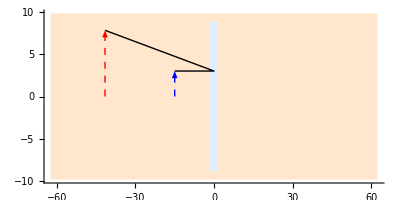

```mathematica
SingleRayGraphic[source_List,image_List,θ_]:=Module[{obj,h1,img,h2,intx,inty,gh,gw,lw},
{intx,inty}=LensIntercept[source,θ];
{obj,h1}=source;
{img,h2}=image;
gh=Abs[inty];
If[Abs[h1]>gh,gh=Abs[h1]];
If[Abs[h2]>gh,gh=Abs[h2]];
gw=Abs[obj];
If[Abs[img]>gw,gw=Abs[img]];
gw=gw*1.5;
lw=gw/40;
Graphics[{LightOrange,Rectangle[{-gw,-gh-2},{gw,gh+2}],LightBlue,Rectangle[{-lw,-gh-1},{lw,gh+1}],Black,Line[{{-obj,h1},{intx,inty},{img,h2}}],Blue,Dashed,Arrow[{{-obj,0},{-obj,h1}}],Red,Dashed,Arrow[{{img,0},{img,h2}}]},Axes->True, AspectRatio->1/2]
]
hold=ThinLens[{16,3},26]
SingleRayGraphic[{15,3},hold,0]
```

Single Ray Container Function

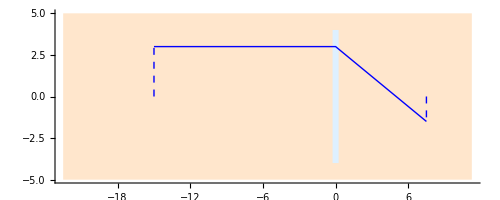

```mathematica
SingleRay[source_List,f_,θ_]:=Module[{image},
image=ThinLens[source,f];
SingleRayGraphic[source,image,θ]
]
SingleRay[{15,3},15,0]
```

Ray-Tracing Diagram
A representation of the full ray-tracing diagram for the given system
PARAMETERS:
(Object distance (m),Object height (m))
(Image distance (m), Image height (m))

```mathematica
RayDiagramImage[source_List,image_List]:=Module[{},
Graphics[{LightBlue,Rectangle[{-.25,},{.25,}]},Axes->True]
]
RayDiagramImage[]
```

#### Interface Functions

### Sandbox